# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
Get["C:\\Users\\Miguel\\Github\\Entropy\\Prethermalization\\QMB.wl"];
```

SetDelayed::write: Tag Commutator in Commutator[A_,B_] is Protected.

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
Clear[haar];
haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[]]+I RandomVariate[NormalDistribution[]],{2^L}]];
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(La),dimb=2^(Lb),rho},
rho=MatrixPartialTrace[state,2,{dima,dimb}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
pageEntropy[La_,Lb_]:=PolyGamma[0,(2^La)(2^Lb)+1]-PolyGamma[0,(2^Lb)+1]-((2^La)-1)/(2*(2^Lb));
```

# Closed boundary conditions

```mathematica
L=6;
```

```mathematica
Clear[evenEigenvectors,oddEigenvectors];
basis=Tuples[{0,1},L];
(*dim=2^L*)
dim=Length[basis];  
(*Create an association to map each basis state to an index*)
basisIndex=AssociationThread[basis,Range[dim]];
(*Step 3:Define a function to convert a basis state into a Hilbert space vector*)
basisVector[state_]:=SparseArray[{basisIndex[state]->1},{dim}];
(*Step 4:Initialize containers for eigenvectors and bookkeeping*)
evenEigenvectors={};  (*Will store even (symmetric) eigenvectors*)
oddEigenvectors={};   (*Will store odd (antisymmetric) eigenvectors*)
processed=ConstantArray[False,dim];  (*Marks which basis states are processed*)
(*Function to compute the reversed state (parity operation on configuration)*)
reverseState[s_List]:=Reverse[s];
(*Step 5:Loop over basis to construct eigenvectors*)
Do[If[processed[[i]],Continue[]];(*Skip states already processed*)(*Retrieve current state and its Hilbert space vector*)state=basis[[i]];
u=basisVector[state];
(*Compute its reflected (reversed) state and corresponding vector*)revState=reverseState[state];
pos=basisIndex[revState];
v=basisVector[revState];
If[i==pos,(*Case:state invariant under parity;already an eigenvector with eigenvalue+1*)AppendTo[evenEigenvectors,u],(*Case:state and its reflected partner are different.Construct symmetric and antisymmetric combinations*)symVec=(u+v)/Sqrt[2];
antiVec=(u-v)/Sqrt[2];
AppendTo[evenEigenvectors,symVec];
AppendTo[oddEigenvectors,antiVec];
(*Mark both states as processed*)processed[[i]]=True;
processed[[pos]]=True;];
(*Ensure the current state is marked as processed if not already*)processed[[i]]=True;,{i,1,dim}];
(*Step 6:Report the dimensions (the number of eigenvectors in each parity sector)*)
Print["Number of even parity eigenvectors: ",Length[evenEigenvectors]];
Print["Number of odd parity eigenvectors: ",Length[oddEigenvectors]];
```

Number of even parity eigenvectors: 36

Number of odd parity eigenvectors: 28

```mathematica
g=0.5;
J=1;
h=1;
H=IsingNNClosedHamiltonian[h,g,J,L];
```

```mathematica
transform=Join[evenEigenvectors,oddEigenvectors];
```

# Constructing the parity operator

```mathematica
(*Number of spins*)
L=12;
(*Local Hilbert space dimension*)
d=2;
(*Generate the computational basis (list of bit strings)*)
basis=Tuples[{0,1},L];
(*The basis will contain 16 elements,each representing a state|s1,s2,s3,s4>*)
(*Convert a given binary state (list) to an integer index*)
ToIndex[state_List]:=FromDigits[state,2]+1;
```

```mathematica
(*For each basis state,find the index of its reflection*)
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,1,Length[basis]}];
(*Convert the mapping into a permutation cycles object*)
permCycles=PermutationCycles[permutation];
(*Construct the reflection symmetry operator as a 16x16 permutation matrix*)
R=PermutationMatrix[permCycles,d^L];
```

```mathematica
{eigenvalR,eigenvecR}=Transpose[Sort[Transpose[Eigensystem[R]]]];
```

```mathematica
g=0.01;
J=1;
h=1;
H=IsingNNClosedHamiltonian[h,g,J,L];
```

```mathematica
Reven=(1/2)(IdentityMatrix[2^L]+R);
Rodd=(1/2)(IdentityMatrix[2^L]-R);
```

```mathematica
evenH=Reven.H.Reven;
oddH=Rodd.H.Rodd;
```

```mathematica
{val,vec}=Transpose[Sort[Transpose[Eigensystem[evenH]]]];
{val2,vec2}=Transpose[Sort[Transpose[Eigensystem[oddH]]]];
```

```mathematica
val//Chop
```

{-5.22913,-4.82565,-2.16479,-2.0001,0,0,0,0,0,0,0,0,0.828402,2.0001,2.16489,5.22628}

```mathematica
val2//Chop
```

{-2.0001,-0.828839,0,0,0,0,0,0,0,0,0,0,0,0.0003998,2.0001,4.82844}

```mathematica
Table[ConjugateTranspose[i].R.i,{i,Chop[vec]}]
Table[ConjugateTranspose[i].R.i,{i,Chop[vec2]}]
```

{1.,1.,1.,1.,-0.365817,-0.9366,-0.754511,-0.920222,-0.41081,0.2652,-0.277173,-0.600068,1.,1.,1.,1.}

{-1.,-1.,0.941977,-0.301978,0.982395,0.927931,1.,0.99989,1.,1.,1.,0.849753,0.600032,-1.,-1.,-1.}

```mathematica
{evalR,evecR}=Eigensystem[R];
```

```mathematica
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
```

```mathematica
Beven//Dimensions
```

{16,10}

```mathematica
Bodd//Dimensions
```

{16,6}

```mathematica
H//Dimensions
```

{16,16}

```mathematica
(*Form the change-of-basis matrix for the even sector*)
Beven=Transpose[evenBasis];
(*The projected even sector Hamiltonian is then:*)
Heven=ConjugateTranspose[Beven].H.Beven;
(*Similarly for the odd sector*)
Bodd=Transpose[oddBasis];
Hodd=ConjugateTranspose[Bodd].H.Bodd;
Peven=ConjugateTranspose[Beven].ope.Beven;
Podd=ConjugateTranspose[Bodd].ope.Bodd;
```

```mathematica
{evenEigs,evenEigVecs}=Eigensystem[Heven];
{oddEigs,oddEigVecs}=Eigensystem[Hodd];
```

```mathematica
evenEigVecs//Dimensions
oddEigVecs//Dimensions
```

{10,10}

{6,6}

```mathematica
Table[Conjugate[i].Peven.i,{i,evenEigVecs}]
Table[Conjugate[i].Podd.i,{i,oddEigVecs}]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

{-1.,-1.,-1.,-1.,-1.,-1.}

```mathematica
Table[Conjugate[i].Heven.i,{i,evenEigVecs}]//Dimensions
val//Dimensions
```

{10}

{16}

```mathematica
Table[Conjugate[i].Heven.i,{i,evenEigVecs}]//Chop//Sort//TableForm
```

-5.22913
-4.82565
-2.16479
-2.0001
0
0
0.828402
2.0001
2.16489
5.22628

```mathematica
Table[Conjugate[i].Hodd.i,{i,oddEigVecs}]//Chop//Sort//TableForm
```

-2.0001
-0.828839
0
0.0003998
2.0001
4.82844

```mathematica
Eigenvalues[IsingNNClosedHamiltonian[h,g,J,L]]//Chop//Sort//TableForm
```

-5.22913
-4.82565
-2.16479
-2.0001
-2.0001
-0.828839
0
0
0
0.0003998
0.828402
2.0001
2.0001
2.16489
4.82844
5.22628

# Parity eigenvectors

```mathematica
L=10;
```

```mathematica
Clear[evenEigenvectors,oddEigenvectors];
basis=Tuples[{0,1},L];
(*dim=2^L*)
dim=Length[basis];  
(*Create an association to map each basis state to an index*)
basisIndex=AssociationThread[basis,Range[dim]];
(*Step 3:Define a function to convert a basis state into a Hilbert space vector*)
basisVector[state_]:=SparseArray[{basisIndex[state]->1},{dim}];
(*Step 4:Initialize containers for eigenvectors and bookkeeping*)
evenEigenvectors={};  (*Will store even (symmetric) eigenvectors*)
oddEigenvectors={};   (*Will store odd (antisymmetric) eigenvectors*)
processed=ConstantArray[False,dim];  (*Marks which basis states are processed*)
(*Function to compute the reversed state (parity operation on configuration)*)
reverseState[s_List]:=Reverse[s];
(*Step 5:Loop over basis to construct eigenvectors*)
Do[If[processed[[i]],Continue[]];(*Skip states already processed*)(*Retrieve current state and its Hilbert space vector*)state=basis[[i]];
u=basisVector[state];
(*Compute its reflected (reversed) state and corresponding vector*)revState=reverseState[state];
pos=basisIndex[revState];
v=basisVector[revState];
If[i==pos,(*Case:state invariant under parity;already an eigenvector with eigenvalue+1*)
AppendTo[evenEigenvectors,u],(*Case:state and its reflected partner are different.Construct symmetric and antisymmetric combinations*)
symVec=(u+v)/Sqrt[2];
antiVec=(u-v)/Sqrt[2];
AppendTo[evenEigenvectors,symVec];
AppendTo[oddEigenvectors,antiVec];
(*Mark both states as processed*)processed[[i]]=True;
processed[[pos]]=True;];
(*Ensure the current state is marked as processed if not already*)processed[[i]]=True;,{i,1,dim}];
(*Step 6:Report the dimensions (the number of eigenvectors in each parity sector)*)
Print["Number of even parity eigenvectors: ",Length[evenEigenvectors]];
Print["Number of odd parity eigenvectors: ",Length[oddEigenvectors]];
```

Number of even parity eigenvectors: 528

Number of odd parity eigenvectors: 496

```mathematica
g=1;
J=1;
h=1.0;
H=IsingNNClosedHamiltonian[h,g,J,L];
```

```mathematica
transform=Join[evenEigenvectors,oddEigenvectors];
```

```mathematica
MatrixPlot[H,PlotRange->800]
MatrixPlot[transform.H.ConjugateTranspose[transform],PlotRange->800,PlotTheme->"Detailed"]
```

-Graphics-

-Graphics-

```mathematica
evenope=Sum[Dyad[i],{i,evenEigenvectors}];
oddope=Sum[-Dyad[i],{i,oddEigenvectors}];
ope=evenope+oddope;
```

```mathematica
newH=transform.H.ConjugateTranspose[transform];
```

```mathematica
newH//Dimensions
```

{1024,1024}

```mathematica
evenEigenvectors//Length
oddEigenvectors//Length
```

528

496

```mathematica
evenH=newH[[1;;Length[evenEigenvectors],1;;Length[evenEigenvectors]]];
oddH=newH[[Length[evenEigenvectors]+1;;-1,Length[evenEigenvectors]+1;;-1]];
evenH//Dimensions
oddH//Dimensions
```

{528,528}

{496,496}

```mathematica
MatrixPlot[evenH]
MatrixPlot[oddH]
```

-Graphics-

-Graphics-

```mathematica
{evenval,evenvec}=Transpose[Sort[Transpose[Eigensystem[evenH]]]];
{oddval,oddvec}=Transpose[Sort[Transpose[Eigensystem[oddH]]]];
```

```mathematica
MeanLevelSpacingRatio[evenval]
MeanLevelSpacingRatio[oddval]
```

0.412485

0.39634

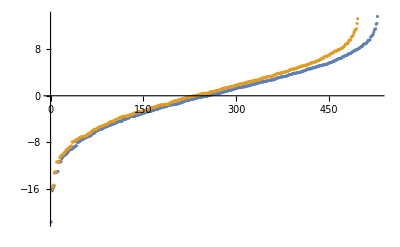

```mathematica
ListPlot[{evenval,oddval},PlotRange->All]
```

```mathematica
g=1;
J=1;
h=1.0;
H=IsingNNClosedHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[H]]]];
```

# <r>

```mathematica
L=12;
```

```mathematica
Clear[evenEigenvectors,oddEigenvectors];
basis=Tuples[{0,1},L];
(*dim=2^L*)
dim=Length[basis];  
(*Create an association to map each basis state to an index*)
basisIndex=AssociationThread[basis,Range[dim]];
(*Step 3:Define a function to convert a basis state into a Hilbert space vector*)
basisVector[state_]:=SparseArray[{basisIndex[state]->1},{dim}];
(*Step 4:Initialize containers for eigenvectors and bookkeeping*)
evenEigenvectors={};  (*Will store even (symmetric) eigenvectors*)
oddEigenvectors={};   (*Will store odd (antisymmetric) eigenvectors*)
processed=ConstantArray[False,dim];  (*Marks which basis states are processed*)
(*Function to compute the reversed state (parity operation on configuration)*)
reverseState[s_List]:=Reverse[s];
(*Step 5:Loop over basis to construct eigenvectors*)
Do[If[processed[[i]],Continue[]];(*Skip states already processed*)(*Retrieve current state and its Hilbert space vector*)state=basis[[i]];
u=basisVector[state];
(*Compute its reflected (reversed) state and corresponding vector*)revState=reverseState[state];
pos=basisIndex[revState];
v=basisVector[revState];
If[i==pos,(*Case:state invariant under parity;already an eigenvector with eigenvalue+1*)
AppendTo[evenEigenvectors,u],(*Case:state and its reflected partner are different.Construct symmetric and antisymmetric combinations*)
symVec=(u+v)/Sqrt[2];
antiVec=(u-v)/Sqrt[2];
AppendTo[evenEigenvectors,symVec];
AppendTo[oddEigenvectors,antiVec];
(*Mark both states as processed*)processed[[i]]=True;
processed[[pos]]=True;];
(*Ensure the current state is marked as processed if not already*)processed[[i]]=True;,{i,1,dim}];
(*Step 6:Report the dimensions (the number of eigenvectors in each parity sector)*)
Print["Number of even parity eigenvectors: ",Length[evenEigenvectors]];
Print["Number of odd parity eigenvectors: ",Length[oddEigenvectors]];
```

Number of even parity eigenvectors: 2080

Number of odd parity eigenvectors: 2016

```mathematica
2^12
```

4096

```mathematica
h=1;
J=1;
```

```mathematica
glist=Range[0.01,2.0,0.01];
```

```mathematica
δ=7;
```

```mathematica
data={};
Do[
H=IsingNNClosedHamiltonian[h,g,J,L];
transform=Join[evenEigenvectors,oddEigenvectors];
newH=transform.H.ConjugateTranspose[transform];
evenH=newH[[1;;Length[evenEigenvectors],1;;Length[evenEigenvectors]]];
oddH=newH[[Length[evenEigenvectors]+1;;-1,Length[evenEigenvectors]+1;;-1]];
{evenval,evenvec}=Transpose[Sort[Transpose[Eigensystem[evenH]]]];
{oddval,oddvec}=Transpose[Sort[Transpose[Eigensystem[oddH]]]];
(*reducedvaleven=Select[evenval,-δ<=#<=δ&];
reducedvalodd=Select[oddval,-δ<=#<=δ&];*)
AppendTo[data,{{g,MeanLevelSpacingRatio[evenval]},{g,MeanLevelSpacingRatio[oddval]}}];
,{g,glist}];
Export["rvalues_closed_chain_bothparities_L_12_h_1_g_0.01_2_nodelta.m",data];
```

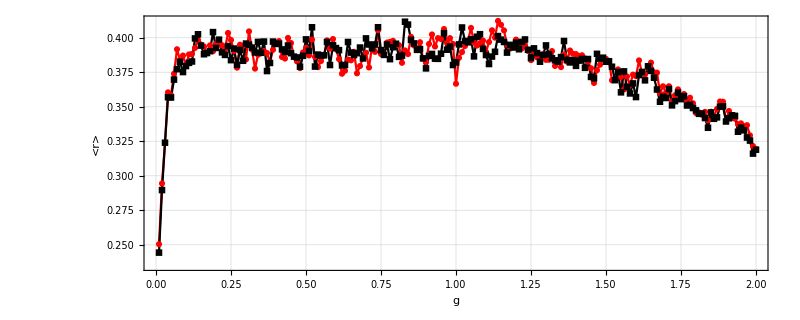

```mathematica
(*CLOSED CHAIN*)
ListPlot[{Transpose[{glist,data[[All,1]][[All,2]]}],Transpose[{glist,data[[All,2]][[All,2]]}]},PlotRange->All,PlotStyle->{Red,Black},PlotTheme->"Detailed",FrameLabel->{Style["g",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4]
```

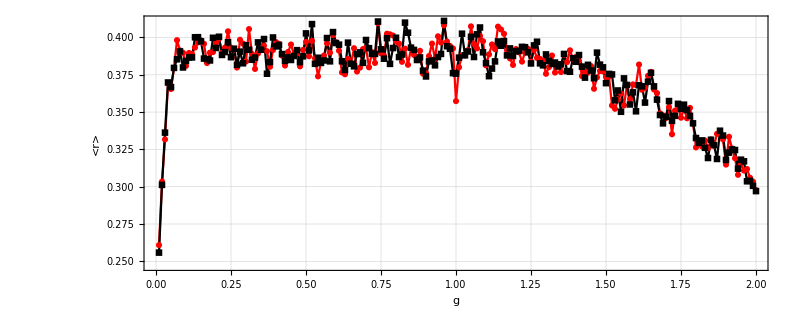

```mathematica
(*CLOSED CHAIN*)
ListPlot[{Transpose[{glist,data[[All,1]][[All,2]]}],Transpose[{glist,data[[All,2]][[All,2]]}]},PlotRange->All,PlotStyle->{Red,Black},PlotTheme->"Detailed",FrameLabel->{Style["g",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4]
```

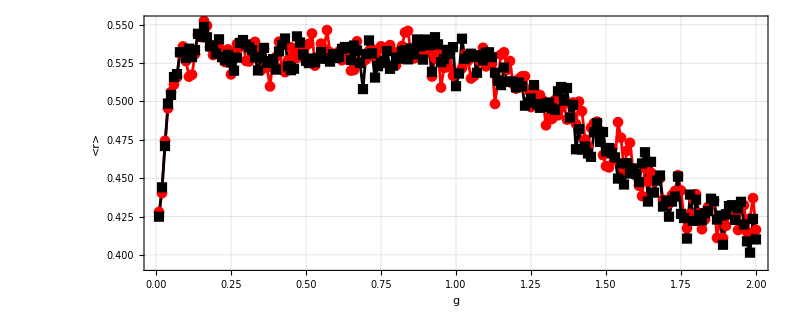

```mathematica
(*OPEN CHAIN*)
ListPlot[{Transpose[{glist,data[[All,1]][[All,2]]}],Transpose[{glist,data[[All,2]][[All,2]]}]},PlotRange->All,PlotStyle->{Red,Black},PlotTheme->"Detailed",FrameLabel->{Style["g",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4]
```

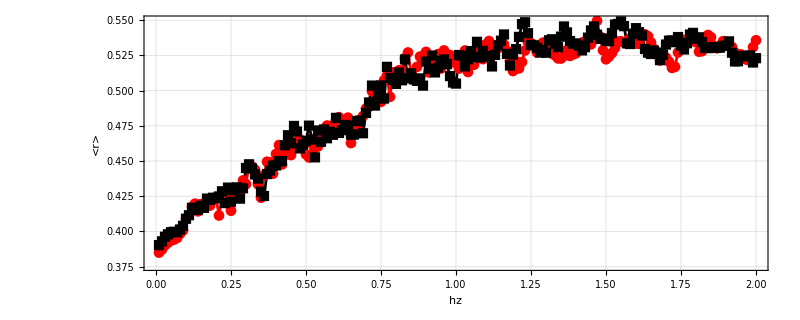

```mathematica
(*OPEN CHAIN*)
ListPlot[{data[[All,1]],data[[All,2]]},PlotRange->All,PlotStyle->{Red,Black},PlotTheme->"Detailed",FrameLabel->{Style["hz",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4]
```

```mathematica
h=1.0;
g=2.0;
H=IsingNNOpenHamiltonian[h,g,J,L];
transform=Join[evenEigenvectors,oddEigenvectors];
newH=transform.H.ConjugateTranspose[transform];
evenH=newH[[1;;Length[evenEigenvectors],1;;Length[evenEigenvectors]]];
oddH=newH[[Length[evenEigenvectors]+1;;-1,Length[evenEigenvectors]+1;;-1]];
{evenval,evenvec}=Transpose[Sort[Transpose[Eigensystem[evenH]]]];
{oddval,oddvec}=Transpose[Sort[Transpose[Eigensystem[oddH]]]];
```

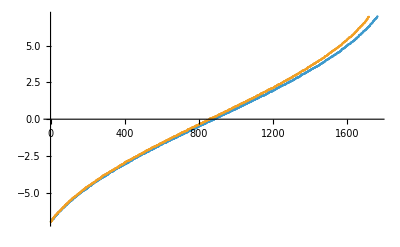

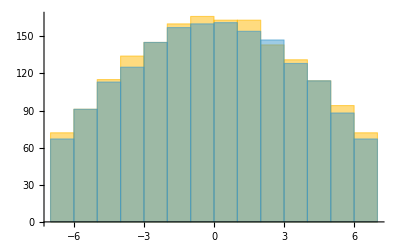

0.427987

0.424896

```mathematica
δ=7;
ListPlot[{Select[evenval,-δ<=#<=δ&],Select[oddval,-δ<=#<=δ&]}]
Histogram[{Select[evenval,-δ<=#<=δ&],Select[oddval,-δ<=#<=δ&]}]
MeanLevelSpacingRatio[Select[evenval,-δ<=#<=δ&]]
MeanLevelSpacingRatio[Select[oddval,-δ<=#<=δ&]]
```

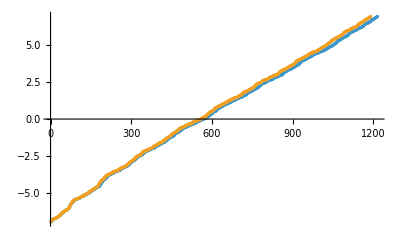

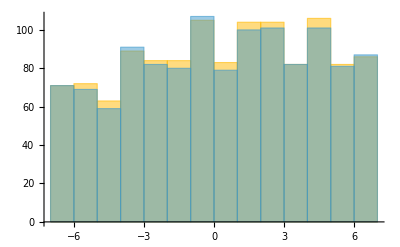

0.416349

0.410082

```mathematica
δ=7;
ListPlot[{Select[evenval,-δ<=#<=δ&],Select[oddval,-δ<=#<=δ&]}]
Histogram[{Select[evenval,-δ<=#<=δ&],Select[oddval,-δ<=#<=δ&]}]
MeanLevelSpacingRatio[Select[evenval,-δ<=#<=δ&]]
MeanLevelSpacingRatio[Select[oddval,-δ<=#<=δ&]]
```

## Spectrum

```mathematica
L=12;
```

```mathematica
J=1;
h=1;
g=0.01;
H=IsingNNClosedHamiltonian[h,g,J,L];
```

```mathematica
(*Generate the computational basis (list of bit strings)*)
basis=Tuples[{0,1},L];
(*The basis will contain 16 elements,each representing a state|s1,s2,s3,s4>*)
(*Convert a given binary state (list) to an integer index*)
ToIndex[state_List]:=FromDigits[state,2]+1;
(*For each basis state,find the index of its reflection*)
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,1,Length[basis]}];
(*Convert the mapping into a permutation cycles object*)
permCycles=PermutationCycles[permutation];
(*Construct the reflection symmetry operator as a 16x16 permutation matrix*)
R=PermutationMatrix[permCycles,2^L];
```

```mathematica
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
```

```mathematica
(*Form the change-of-basis matrix for the even sector*)
Beven=Transpose[evenBasis];
(*The projected even sector Hamiltonian is then:*)
Heven=ConjugateTranspose[Beven].H.Beven;
(*Similarly for the odd sector*)
Bodd=Transpose[oddBasis];
Hodd=ConjugateTranspose[Bodd].H.Bodd;
```

```mathematica
Peven=ConjugateTranspose[Beven].N[R].Beven;
Podd=ConjugateTranspose[Bodd].R.Bodd;
```

```mathematica
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[Heven]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[Hodd]]]];
```

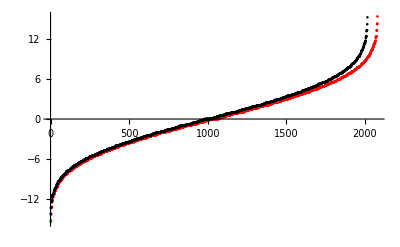

```mathematica
ListPlot[{eveneigenval,oddeigenval},PlotRange->All,PlotStyle->{Red,Black}]
```

```mathematica
MeanLevelSpacingRatio[eveneigenval]
MeanLevelSpacingRatio[oddeigenval]
```

0.250429

0.244335

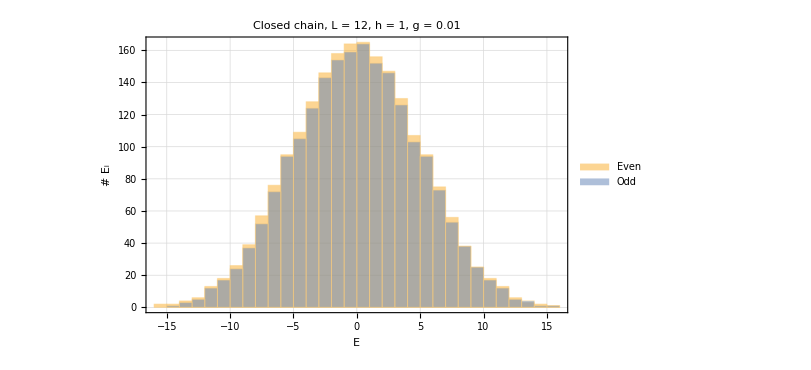

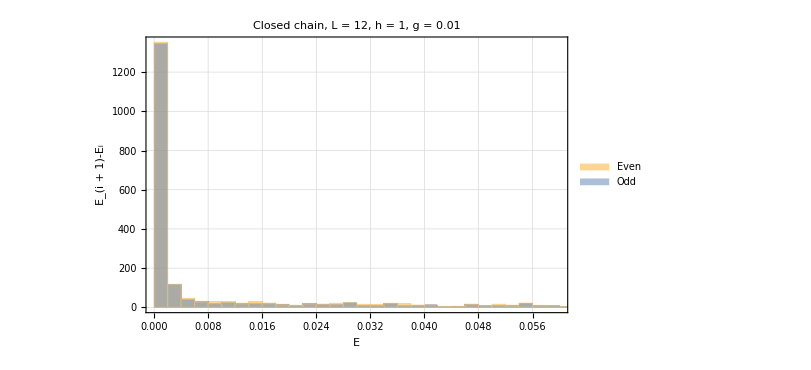

```mathematica
Histogram[{eveneigenval,oddeigenval},PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["Closed chain, L = 12, h = 1, g = 0.01",30,Black],FrameLabel->{Style["E",30,Black],Style["# E_i",30,Black]},FrameStyle->{{25,Black},{25,Black}},ChartLegends->{Style["Even",25,Black],Style["Odd",25,Black]}]
Histogram[{Differences[eveneigenval],Differences[oddeigenval]},PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["Closed chain, L = 12, h = 1, g = 0.01",30,Black],FrameLabel->{Style["E",30,Black],Style["E_(i + 1)-E_i",30,Black]},FrameStyle->{{25,Black},{25,Black}},ChartLegends->{Style["Even",25,Black],Style["Odd",25,Black]}]
```

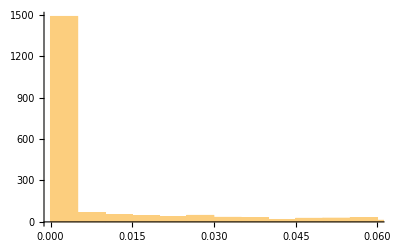

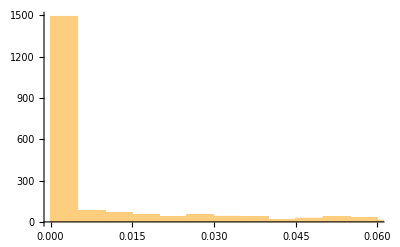

```mathematica
Histogram[Differences[oddeigenval]]
Histogram[Differences[eveneigenval]]
```

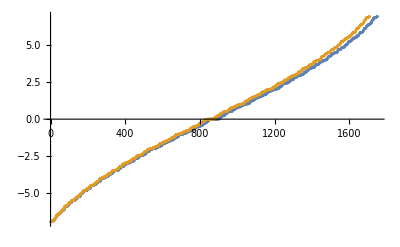

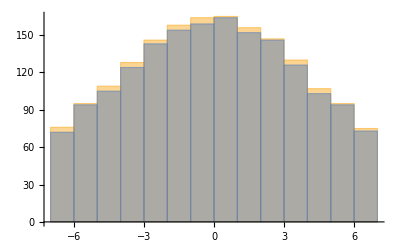

0.260857

0.255822

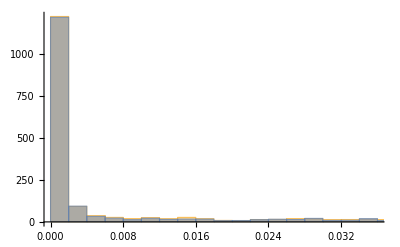

```mathematica
δ=7;
ListPlot[{Select[eveneigenval,-δ<=#<=δ&],Select[oddeigenval,-δ<=#<=δ&]}]
Histogram[{Select[eveneigenval,-δ<=#<=δ&],Select[oddeigenval,-δ<=#<=δ&]}]
MeanLevelSpacingRatio[Select[eveneigenval,-δ<=#<=δ&]]
MeanLevelSpacingRatio[Select[oddeigenval,-δ<=#<=δ&]]
Histogram[{Differences[Select[eveneigenval,-δ<=#<=δ&]],Differences[Select[oddeigenval,-δ<=#<=δ&]]}]
```

```mathematica
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[H]]]];
```

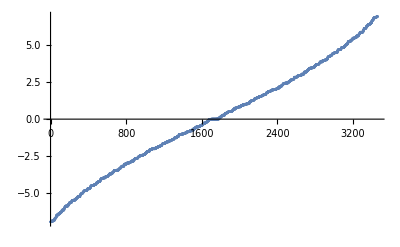

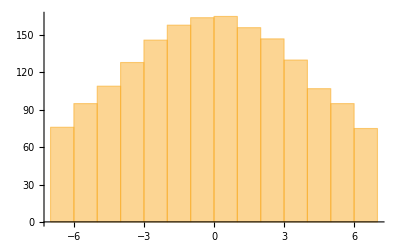

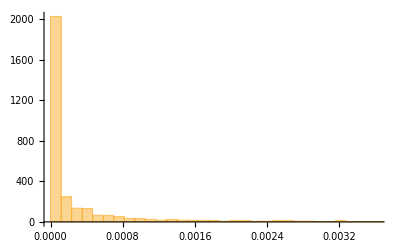

```mathematica
δ=7;
ListPlot[{Select[eigenval,-δ<=#<=δ&]}]
Histogram[{Select[evenval,-δ<=#<=δ&]}]
Histogram[{Differences[Select[eigenval,-δ<=#<=δ&]]}]
```

# Numerical precision

```mathematica
Clear[rhot];
rhot[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{ck=Conjugate[eigenvec].ini,rho,dima=2^(La),dimb=2^(Lb),rhod,rhond,allrho,totalrho},
(*rhond=Table[If[i!=j,ck[[i]]*Conjugate[ck[[j]]*Exp[-I*Chop[eigenval[[i]]-eigenval[[j]]]*t]],ck[[i]]*Conjugate[ck[[j]]]],{i,2^L},{j,2^L}];*)
rhond=Table[If[i!=j,If[Abs[Chop[eigenval[[i]]-eigenval[[j]]]]<=10^-8,ck[[i]]*Conjugate[ck[[j]]],ck[[i]]*Conjugate[ck[[j]]]Exp[-I*Chop[eigenval[[i]]-eigenval[[j]]]*t]],ck[[i]]*Conjugate[ck[[j]]]],{i,2^L},{j,2^L}];
totalrho=Transpose[eigenvec].(rhond).Conjugate[eigenvec]
(*MatrixPartialTrace[totalrho,2,{dima,dimb}]*)
];
```

```mathematica
L=8;
g=0.01;
J=1;
h=1;
H=IsingNNClosedHamiltonian[h,g,J,L];
```

```mathematica
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[H]]]];
```

```mathematica
ini=RandomChainProductState[L];
```

```mathematica
tlist=Table[10^i,{i,-2,17,0.01}];
tlist//Length
```

1901

```mathematica
rhos=ParallelTable[rhot[L,4,4,ini,eigenval,eigenvec,t],{t,tlist},DistributedContexts->Full];
```

```mathematica
trazas=ParallelTable[Tr[i],{i,rhos},DistributedContexts->Full];
```

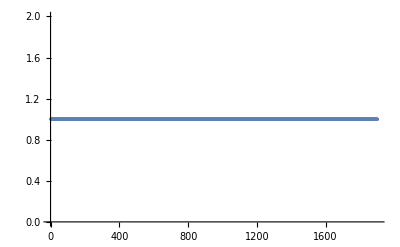

```mathematica
ListPlot[trazas]
```

```mathematica
schmidt=ParallelTable[Eigenvalues[Chop[i]],{i,rhos},DistributedContexts->Full];
```

```mathematica
schmidttrace=ParallelTable[Total[i],{i,schmidt},DistributedContexts->Full];
```

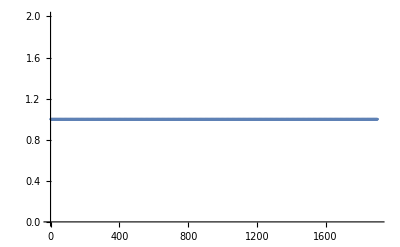

```mathematica
ListPlot[schmidttrace]
```

```mathematica
purity=ParallelTable[Tr[i.i],{i,rhos},DistributedContexts->Full];
```

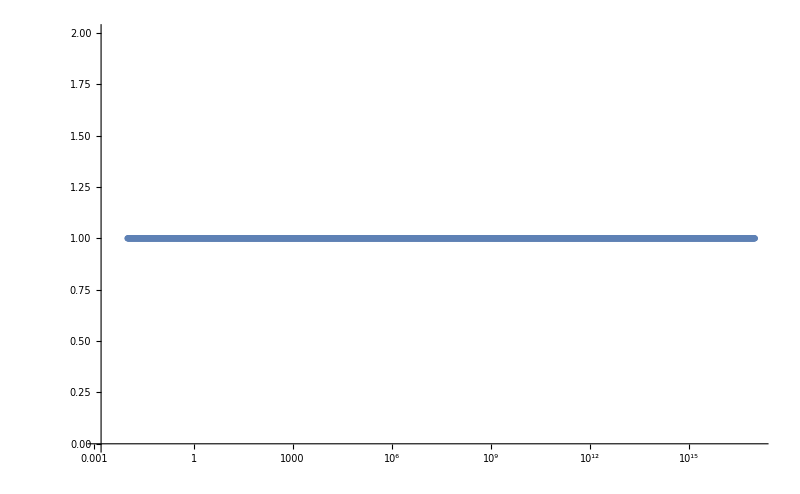

```mathematica
ListLogLinearPlot[Transpose[{tlist,purity}],PlotRange->All,ImageSize->800]
```

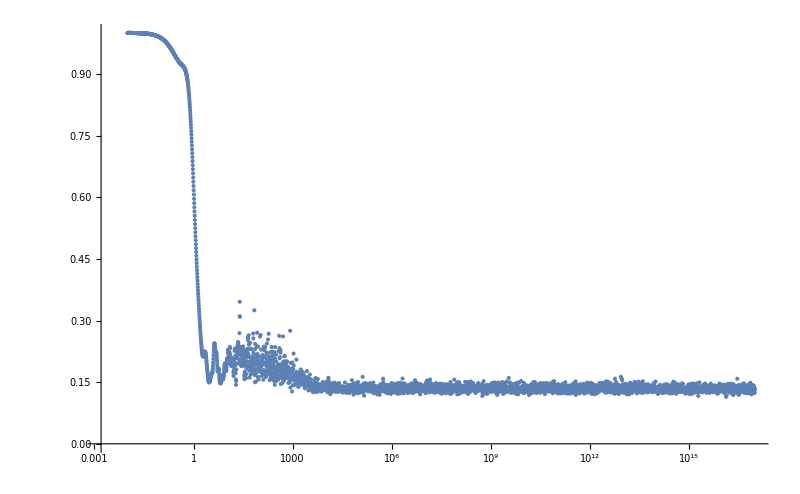

```mathematica
ListLogLinearPlot[Transpose[{tlist,purity}],PlotRange->All,ImageSize->800]
```

```mathematica
Clear[vnentropy];
vnentropy[eigVals_List]:=-Total[Map[If[#==0,0,# Log[#]]&,Chop[eigVals]]];
```

```mathematica
entropies=ParallelTable[vnentropy[Chop[i]],{i,schmidt}];
```

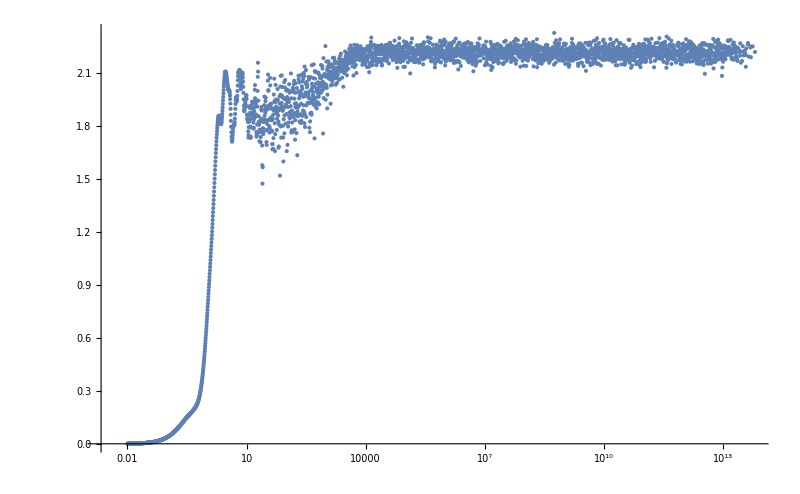

```mathematica
ListLogLinearPlot[Transpose[{tlist,entropies}],PlotRange->All,ImageSize->800]
```

```mathematica
Transpose[{schmidt[[-1]],Chop[schmidt[[-1]]]}]//TableForm
```

0.195325+1.22794×10^-17 ⅈ | 0.195325
0.162624+2.01404×10^-18 ⅈ | 0.162624
0.141689-6.88549×10^-18 ⅈ | 0.141689
0.121991-1.20497×10^-17 ⅈ | 0.121991
0.0977091-8.83702×10^-18 ⅈ | 0.0977091
0.0925291-4.15051×10^-18 ⅈ | 0.0925291
0.072437-1.23786×10^-17 ⅈ | 0.072437
0.0647987-1.14464×10^-17 ⅈ | 0.0647987
0.0491647+4.77118×10^-18 ⅈ | 0.0491647
0.0341457+7.4791×10^-18 ⅈ | 0.0341457
-0.0302543+9.50542×10^-18 ⅈ | -0.0302543
-0.0237198-4.63612×10^-18 ⅈ | -0.0237198
0.0184225-4.79606×10^-18 ⅈ | 0.0184225
0.00866178+5.35066×10^-18 ⅈ | 0.00866178
-0.00615297-1.27491×10^-17 ⅈ | -0.00615297
0.000629459+2.26848×10^-18 ⅈ | 0.000629459

```mathematica
entropies[[-10;;-1]]
```

{2.06479+0.281315 ⅈ,2.16708+0.224813 ⅈ,2.19425+0.169999 ⅈ,2.1253+0.282422 ⅈ,2.15567+0.176319 ⅈ,2.13343+0.204193 ⅈ,2.16566+0.220009 ⅈ,2.14434+0.217531 ⅈ,2.21378+0.145259 ⅈ,2.11972+0.188895 ⅈ}

```mathematica
Transpose[{Tr[rhos[[-1]].rhos[[-1]]],Chop[Tr[rhos[[-1]].rhos[[-1]]]]}]//TableForm
```

0.132624-2.49107×10^-18 ⅈ
0.132624

```mathematica
rhos[[-1]].rhos[[-1]]//Tr
```

0.132624-2.49107×10^-18 ⅈ

```mathematica
schmidt//Dimensions
```

{1901,256}

```mathematica
tlist[[1000]]
```

9.77237×10^7

```mathematica
schmidt[[1100]]//Chop
schmidt[[-1]]//Chop
```

{1.,1.72248×10^-7,-1.72248×10^-7,-1.60019×10^-7,1.60019×10^-7,-1.33313×10^-7,1.33313×10^-7,1.28119×10^-7,-1.28119×10^-7,1.13205×10^-7,-1.13205×10^-7,1.03632×10^-7,-1.03632×10^-7,1.00452×10^-7,-1.00452×10^-7,8.68743×10^-8,-8.68743×10^-8,8.20005×10^-8,-8.20005×10^-8,7.8347×10^-8,-7.83469×10^-8,7.17604×10^-8,-7.17604×10^-8,-6.87981×10^-8,6.87981×10^-8,-6.47942×10^-8,6.47942×10^-8,-6.21512×10^-8,6.21512×10^-8,5.60617×10^-8,-5.60617×10^-8,5.37771×10^-8,-5.37771×10^-8,-5.06029×10^-8,5.06029×10^-8,-4.85923×10^-8,4.85923×10^-8,-4.73136×10^-8,4.73135×10^-8,4.44209×10^-8,-4.44209×10^-8,-4.22432×10^-8,4.22432×10^-8,-4.18238×10^-8,4.18237×10^-8,4.08788×10^-8,-4.08788×10^-8,-4.02061×10^-8,4.02061×10^-8,3.85249×10^-8,-3.85249×10^-8,-3.75682×10^-8,3.75682×10^-8,3.64284×10^-8,-3.64284×10^-8,-3.40227×10^-8,3.40227×10^-8,-3.32374×10^-8,3.32374×10^-8,-3.18712×10^-8,3.18712×10^-8,-3.14042×10^-8,3.14042×10^-8,3.01861×10^-8,-3.01861×10^-8,-2.87089×10^-8,2.87089×10^-8,-2.73559×10^-8,2.73559×10^-8,2.61706×10^-8,-2.61706×10^-8,2.5469×10^-8,-2.5469×10^-8,2.38504×10^-8,-2.38504×10^-8,2.33483×10^-8,-2.33483×10^-8,-2.17272×10^-8,2.17272×10^-8,-2.14353×10^-8,2.14353×10^-8,2.04155×10^-8,-2.04155×10^-8,1.9546×10^-8,-1.9546×10^-8,1.85526×10^-8,-1.85526×10^-8,1.82756×10^-8,-1.82756×10^-8,1.74747×10^-8,-1.74746×10^-8,1.69362×10^-8,-1.69362×10^-8,1.60977×10^-8,-1.60977×10^-8,1.59843×10^-8,-1.59843×10^-8,1.5474×10^-8,-1.5474×10^-8,1.47245×10^-8,-1.47245×10^-8,1.43427×10^-8,-1.43427×10^-8,-1.4064×10^-8,1.4064×10^-8,-1.36523×10^-8,1.36523×10^-8,1.33852×10^-8,-1.33852×10^-8,1.25953×10^-8,-1.25953×10^-8,-1.24571×10^-8,1.24571×10^-8,1.21428×10^-8,-1.21428×10^-8,-1.1448×10^-8,1.1448×10^-8,1.10769×10^-8,-1.10769×10^-8,1.07824×10^-8,-1.07824×10^-8,1.06537×10^-8,-1.06537×10^-8,1.01923×10^-8,-1.01923×10^-8,9.92474×10^-9,-9.92474×10^-9,9.61384×10^-9,-9.61383×10^-9,-9.24647×10^-9,9.24647×10^-9,-8.70989×10^-9,8.70989×10^-9,8.39186×10^-9,-8.39186×10^-9,-8.27058×10^-9,8.27058×10^-9,8.09464×10^-9,-8.09464×10^-9,-7.80398×10^-9,7.80398×10^-9,7.56814×10^-9,-7.56814×10^-9,-7.34088×10^-9,7.34088×10^-9,-7.14538×10^-9,7.14538×10^-9,6.8148×10^-9,-6.8148×10^-9,6.56267×10^-9,-6.56267×10^-9,-6.50524×10^-9,6.50524×10^-9,6.06193×10^-9,-6.06193×10^-9,5.91996×10^-9,-5.91996×10^-9,-5.82261×10^-9,5.82261×10^-9,5.50573×10^-9,-5.50573×10^-9,5.32383×10^-9,-5.32383×10^-9,5.2551×10^-9,-5.2551×10^-9,4.75003×10^-9,-4.75003×10^-9,4.57135×10^-9,-4.57135×10^-9,-4.35601×10^-9,4.35601×10^-9,4.20377×10^-9,-4.20377×10^-9,4.06253×10^-9,-4.06253×10^-9,3.69549×10^-9,-3.69549×10^-9,-3.6562×10^-9,3.6562×10^-9,-3.58368×10^-9,3.58368×10^-9,3.25642×10^-9,-3.25642×10^-9,3.14809×10^-9,-3.14809×10^-9,2.88407×10^-9,-2.88407×10^-9,-2.79444×10^-9,2.79444×10^-9,2.6924×10^-9,-2.6924×10^-9,2.52651×10^-9,-2.52651×10^-9,2.36275×10^-9,-2.36275×10^-9,2.25902×10^-9,-2.25902×10^-9,2.10634×10^-9,-2.10634×10^-9,1.99974×10^-9,-1.99974×10^-9,1.83289×10^-9,-1.83289×10^-9,1.74207×10^-9,-1.74206×10^-9,1.6678×10^-9,-1.6678×10^-9,1.55382×10^-9,-1.55382×10^-9,1.52661×10^-9,-1.52661×10^-9,1.39379×10^-9,-1.39379×10^-9,1.31552×10^-9,-1.31552×10^-9,1.1671×10^-9,-1.1671×10^-9,-1.06118×10^-9,1.06118×10^-9,9.80695×10^-10,-9.80694×10^-10,-8.94079×10^-10,8.94079×10^-10,8.43002×10^-10,-8.43001×10^-10,7.53748×10^-10,-7.53747×10^-10,-6.59865×10^-10,6.59864×10^-10,-6.0008×10^-10,6.0008×10^-10,5.15514×10^-10,-5.15513×10^-10,4.70473×10^-10,-4.70472×10^-10,3.54608×10^-10,-3.54607×10^-10,3.36305×10^-10,-3.36305×10^-10,-2.68068×10^-10,2.68068×10^-10,2.50976×10^-10,-2.50976×10^-10,1.96943×10^-10,-1.96942×10^-10,1.33453×10^-10,-1.33452×10^-10,-1.16142×10^-10,1.16141×10^-10,0,0,0,0,0,0,0}

{0.634306,-0.240984,0.185151,-0.183115,0.175523,-0.16079,0.156376,0.141041,-0.138052,-0.131773,0.124981,0.120856,-0.120364,0.113926,-0.109635,0.105147,-0.102715,-0.0971959,0.0969784,0.0951175,0.0931861,-0.0923915,0.0858875,-0.0857403,-0.0825199,0.0812616,-0.0780522,0.0752291,-0.0743637,0.0736457,0.0726165,-0.0719584,0.0698179,-0.0689649,-0.0657109,0.0649071,0.0638634,-0.0629105,0.0620343,-0.0609728,0.0600972,-0.0586829,0.0577669,-0.056,0.055379,0.0545445,-0.0541753,0.0519378,-0.0517595,0.0509964,0.0493752,-0.0491901,0.0489401,-0.0472553,0.0468714,0.0446313,-0.044319,0.0438985,0.0425258,-0.0423741,-0.0418987,0.0410244,0.039472,-0.0394459,0.0390722,-0.0378792,-0.0371828,0.0369994,0.0361247,0.0349538,-0.0347252,-0.0338783,0.0337877,0.0329986,-0.0328642,0.0319598,-0.0317928,0.0308415,0.0303117,-0.0302471,0.0290712,-0.0288724,0.028243,0.0277796,-0.0277427,-0.026525,0.0262921,-0.0261796,0.0258779,-0.0253715,0.0252886,-0.0244698,0.0239888,0.0237546,-0.0234344,0.0230751,-0.0227263,-0.0223879,0.0220082,-0.0216986,0.0212523,-0.0212234,0.0205474,0.0201848,-0.020131,-0.019732,0.0195462,-0.0190413,0.0189274,-0.0184717,0.0182488,-0.0181948,0.0176067,-0.0172917,0.0169567,-0.0165761,0.0165091,-0.0162465,0.016177,-0.0154078,0.0153125,0.0152162,-0.0149111,0.0145712,-0.0143808,-0.0139541,0.0138527,0.0135809,-0.0133744,0.0131152,-0.0128349,0.012407,0.0122982,-0.0121105,0.0120686,-0.0117663,0.0116353,-0.0114396,0.0112186,0.0111198,-0.0108888,-0.0105957,0.0104816,0.00991838,-0.00978199,0.00964806,-0.00946291,-0.00922254,0.00910563,0.00884524,-0.00872489,0.00858567,-0.00837478,-0.00820842,0.00816395,0.00804019,-0.00796826,-0.00776812,0.00769579,0.00737378,-0.00731745,0.00727953,0.0069689,-0.00693667,0.00674498,-0.00666553,0.00654974,-0.00648373,0.00620982,0.00600865,-0.00600455,0.00580028,-0.00576773,0.00534857,-0.00534423,-0.00525635,0.00520865,-0.00510867,0.00496088,-0.00490687,0.00484316,0.00472514,-0.00465565,0.00437442,-0.00431097,0.00428906,0.00409088,-0.00408978,-0.00400083,-0.00388195,0.00381549,-0.00370762,0.00365236,0.00348638,-0.00346954,0.00329994,0.00318809,-0.00318078,-0.00306014,0.00293827,-0.00290866,-0.00280841,0.00268495,-0.00263843,0.00260501,0.00249958,-0.00234374,0.00229891,-0.00227079,-0.00209784,0.00206165,-0.00199306,0.00196382,-0.00185832,0.00180975,-0.00177175,0.00171649,0.00166168,-0.00159351,0.00157,-0.00154353,0.00147867,0.00137203,-0.00136217,-0.00129608,0.00122434,-0.00112135,0.00107262,-0.00100299,-0.000935325,0.000917547,0.000859184,-0.000810326,-0.000786439,0.000734421,0.000683051,-0.000617842,0.000588688,-0.000543095,0.000505335,-0.000481616,0.00041685,0.000374512,-0.000372725,-0.000352038,-0.000293458,0.000292662,0.000236636,-0.000186772,0.000172352,-0.000116945,0.000113922,-0.0000828522,0.0000722994,-0.0000207171,0.000011495}

```mathematica
DiagonalizeMatrix
```